{{{{0.,0.},{0.,0.000459348},{0.142857,0.171961},{0.142857,0.178687},{0.285714,0.230624},{0.285714,0.28084},{0.428571,0.302191},{0.428571,0.341615},{0.571429,0.433203},{0.571429,0.450162},{1.,0.5181},{1.,0.554983},{1.57143,0.610855},{1.57143,0.622168},{2.28571,0.602745},{2.28571,0.656218},{3.,0.651992},{3.,0.706122}}},{{{0.,0.},{0.,0.},{0.142857,0.198718},{0.142857,0.230991},{0.285714,0.301349},{0.285714,0.341286},{0.428571,0.349192},{0.428571,0.390179},{0.571429,0.4375},{0.571429,0.438998},{1.,0.482094},{1.,0.577836},{1.57143,0.593529},{1.57143,0.624273},{2.28571,0.608384},{2.28571,0.661899},{3.,0.634812},{3.,0.715008}}}}

{{{{0.571429,0.445594},{0.571429,0.455019},{0.571429,0.475683},{1.14286,0.2049},{1.14286,0.221119},{1.14286,0.2309},{1.71429,0.103198},{1.71429,0.104663},{1.71429,0.109079}}},{{{1.,0.606946},{1.,0.622896},{1.28571,0.493306},{1.28571,0.522344},{1.57143,0.394139},{1.57143,0.493586},{2.,0.286646},{2.,0.306972},{2.57143,0.173198},{2.57143,0.223916},{3.,0.201035},{3.,0.21637}}},{{{1.,0.631008},{1.,0.679236},{1.57143,0.383775},{1.57143,0.422101},{1.85714,0.358646},{1.85714,0.392652},{2.,0.279817},{2.,0.332502},{2.57143,0.152288},{2.57143,0.185462},{3.,0.139909},{3.,0.224561}}},{{{3.,0.710887},{3.,0.714191},{3.57143,0.395753},{3.57143,0.612321},{3.85714,0.320261},{3.85714,0.385408},{4.14286,0.211316},{4.14286,0.217783},{4.57143,0.136},{4.57143,0.176365},{5.,0.132282},{5.,0.155566}}}}

117508.

8TemMeanKi67Pos.xls

8TemAllKi67Pos.xls

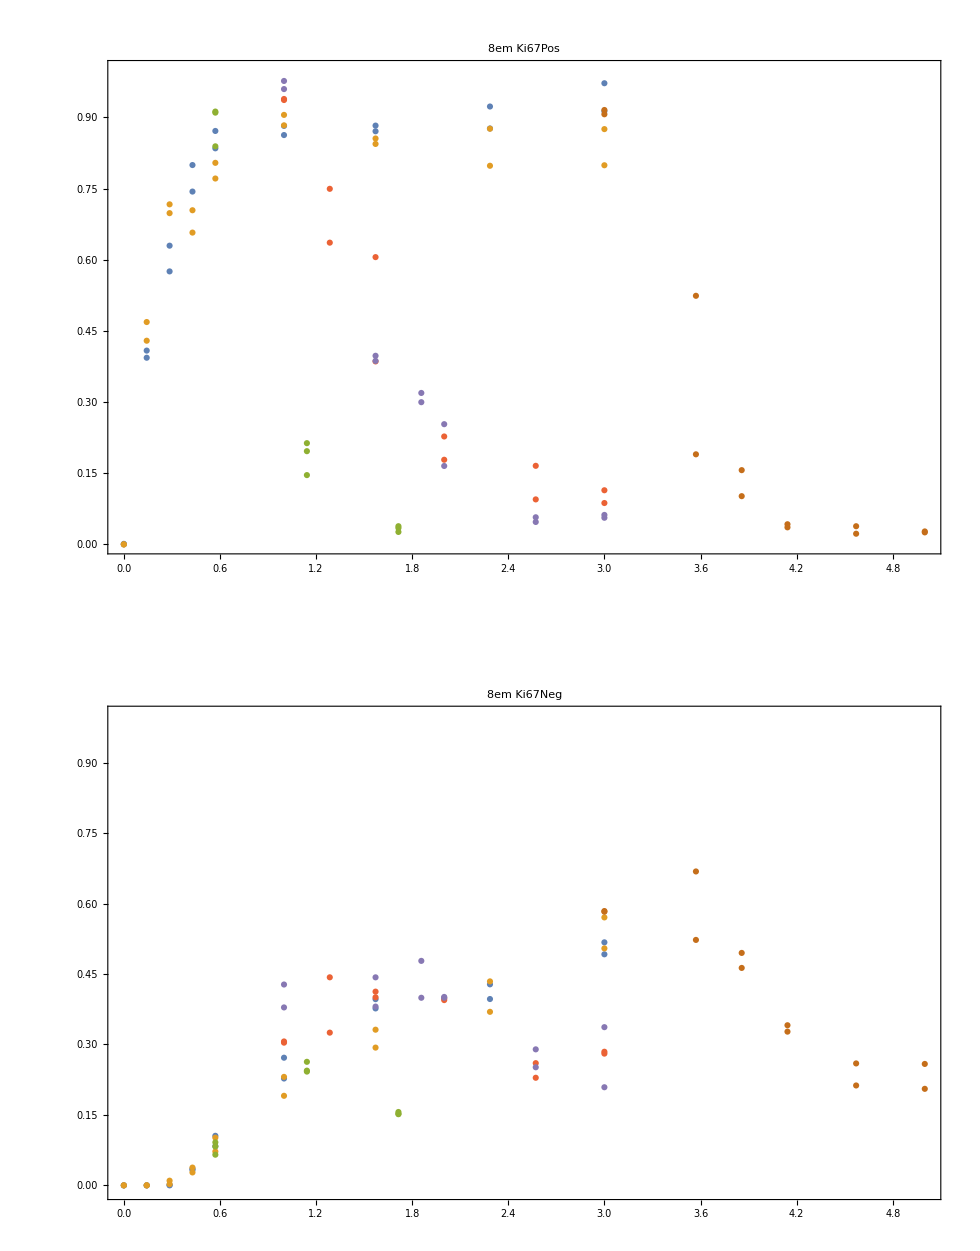

8TemDataImg.pdf

8Tem Brdu+.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
pop="8em";
popSubs={"8em"->"8Tem","8cm"->"8Tcm","4em"->"4Tem","4cm"->"4Tcm"};
upslopes={185,203};
downslopes={184,206,196,197};

eS="expt";
upSheets=Table[eS<>ToString[upslopes[[i]]],{i,1,Length[upslopes]}];
downSheets=Table[eS<>ToString[downslopes[[i]]],{i,1,Length[downslopes]}];
importSheet[sheetName_]:=Import["29AprilRegate.xlsx",{"Sheets",sheetName}];

upData=Table[importSheet[upSheets[[i]]],{i,1,Length[upSheets]}];
downData=Table[importSheet[downSheets[[i]]],{i,1,Length[downSheets]}];


header=upData[[1,1]]; (*assumes all headers are identical - currently verified by eye, not hard only 4 or 5 sheets!*)

KmBmPos=Position[header,"Ki67neg.BrdUneg"][[1,1]];
KmBpPos=Position[header,"Ki67neg.BrdUpos"][[1,1]];

KpBmPos=Position[header,"Ki67pos.BrdUneg"][[1,1]];
KpBpPos=Position[header,"Ki67pos.BrdUpos"][[1,1]];

popPos=Position[header,"population"][[1,1]];
dataTemplate:=ToExpression@Table["x"<>ToString[i]<>"_",{i,1,Length[header]}]
(*drop headers from data*)
upData=Table[Drop[upData[[i]],1],{i,1,Length[upData]}];
downData=Table[Drop[downData[[i]],1],{i,1,Length[downData]}];

upTimeSpot=3;
downTimeSpot=4;

upDataCell=Table[Sort[Cases[upData[[i]],dataTemplate/;x7==pop],#1[[upTimeSpot]]<#2[[upTimeSpot]]&],{i,1,Length[upData]}];
(*delete t=0 points from downslope data*)
downDataCell=Table[Sort[Cases[downData[[i]],dataTemplate/;(x7==pop)&&x3≠0],#1[[downTimeSpot]]<#2[[downTimeSpot]]&],{i,1,Length[downData]}];

upTimes=Table[upDataCell[[i]][[All,upTimeSpot]],{i,1,Length[upDataCell]}];
downOnTimes=Table[downDataCell[[i]][[All,upTimeSpot]],{i,1,Length[downDataCell]}];
downTimes=Table[downDataCell[[i]][[All,downTimeSpot]],{i,1,Length[downDataCell]}];

weekScale=7;
BpFracKp[set_,times_]:=Sort@({times/weekScale,set[[All,KpBpPos]]/(set[[All,KpBpPos]]+set[[All,KpBmPos]])}//Transpose)
BpFracKm[set_,times_]:=Sort@({times/weekScale,set[[All,KmBpPos]]/(set[[All,KmBpPos]]+set[[All,KmBmPos]])}//Transpose)

BPos[set_,times_]:=Sort@({times/weekScale,(set[[All,KmBpPos]]+set[[All,KpBpPos]])/(set[[All,KmBpPos]]+set[[All,KmBmPos]]+set[[All,KpBpPos]]+set[[All,KpBmPos]])}//Transpose)

tempM="KmRatio";
tempP="KpRatio";
outputNamesUp=Table[{tempM<>"UpExpt"<>ToString[upslopes[[i]]],tempP<>"UpExpt"<>ToString[upslopes[[i]]]},{i,1,Length[upSheets]}];

outputNamesDown=Table[{tempM<>"DownExpt"<>ToString[downslopes[[i]]],tempP<>"DownExpt"<>ToString[downslopes[[i]]]},{i,1,Length[downSheets]}];

upExportData=Table[{
BpFracKm[upDataCell[[i]],upTimes[[i]]],
BpFracKp[upDataCell[[i]],upTimes[[i]]]
},{i,1,Length[upSheets]}];
downExportData=Table[{
BpFracKm[downDataCell[[i]],downTimes[[i]]+downOnTimes[[i]]],
BpFracKp[downDataCell[[i]],downTimes[[i]]+downOnTimes[[i]]]
},{i,1,Length[downSheets]}];
bPosUp=Table[{
BPos[upDataCell[[i]],upTimes[[i]]]
},{i,1,Length[upSheets]}]
bPosDown=Table[{
BPos[downDataCell[[i]],downTimes[[i]]+downOnTimes[[i]]]
},{i,1,Length[downSheets]}]
combinedNames=Flatten@Join[outputNamesUp,outputNamesDown];
combinedData=Flatten[Join[upExportData,downExportData],1];

sheetSub=Table[combinedNames[[i]]->combinedData[[i]],{i,1,Length[combinedNames]}];
Export[(pop/.popSubs)<>"BRDU.xls","Sheets"->sheetSub,"Rules"];

posList={KmBmPos,KmBpPos,KpBmPos,KpBpPos};
upTotal=Flatten@Total@Table[upDataCell[[j]][[All,posList[[i]]]],{i,1,Length[posList]},{j,1,Length[upDataCell]}];
downTotal=Flatten@Total@Table[downDataCell[[j]][[All,posList[[i]]]],{i,1,Length[posList]},{j,1,Length[downDataCell]}];
memSizeMean=Mean@Join[upTotal,downTotal]

kPosFrac[set_]:=(set[[All,KpBpPos]]+set[[All,KpBmPos]])/(set[[All,KpBpPos]]+set[[All,KpBmPos]]+set[[All,KmBpPos]]+set[[All,KmBmPos]])

allData=Join[upDataCell,downDataCell];
allKi67=Flatten@Table[kPosFrac[allData[[i]]],{i,1,Length[allData]}];
totalMeanKi67=Mean@allKi67;
Export[(pop/.popSubs)<>"MeanKi67Pos.xls",totalMeanKi67,"xls"]
Export[(pop/.popSubs)<>"AllKi67Pos.xls",allKi67,"xls"]
kM=Join[Table[upExportData[[i,1]],{i,1,Length[upslopes]}],Table[downExportData[[i,1]],{i,1,Length[downslopes]}]];
kP=Join[Table[upExportData[[i,2]],{i,1,Length[upslopes]}],Table[downExportData[[i,2]],{i,1,Length[downslopes]}]];
dataImg=GraphicsGrid[{{ListPlot[kP,Frame->True,PlotLabel->pop<>" Ki67Pos",PlotRange->{0,1}]},{
ListPlot[kM,Frame->True,PlotLabel->pop<>" Ki67Neg",PlotRange->{-0.01,1}]}},Frame->True]
Export[(pop/.popSubs)<>"DataImg.pdf",dataImg,ImageResolution->250]
brduPosImg=ListPlot[Join[Flatten[bPosUp,1],Flatten[bPosDown,1]],Frame->True,PlotRange->{0,1},PlotLabel->pop<>" brdu+%"];
Export[(pop/.popSubs)<>" Brdu+.pdf",brduPosImg]
```